# Anharmonic Chains

Reference: H. Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Subscript[mc, dir]="../../../../mode_coupling_KPZ/calculations/";
```

```mathematica
<<(Subscript[mc, dir]<>"NFH_base.m");
```

```mathematica
(* re-definition adapted to V *)
(* dynamic programming *)
CalculateAverage[f_,{V_,p_,β_},sym_]:=CalculateAverage[f,{V,p,β},sym]=
	If[sym,(* symbolic version *)
		 Integrate[f[x]Exp[-β(V[x]+p x)],{x,(*-∞*)1/2,∞},Assumptions:>{p>0,β>0}]/Integrate[Exp[-β(V[x]+p x)],{x,(*-∞*)1/2,∞},Assumptions:>{p>0,β>0}],
		NIntegrate[f[x]Exp[-β(V[x]+p x)],{x,(*-∞*)1/2,∞}]/NIntegrate[Exp[-β(V[x]+p x)],{x,(*-∞*)1/2,∞}]]
```

## Theoretical framework

```mathematica
(* "shoulder" potential *)
Subscript[V, val][x_]:=If[x<1/2,∞,If[x<1,1,0]]
```

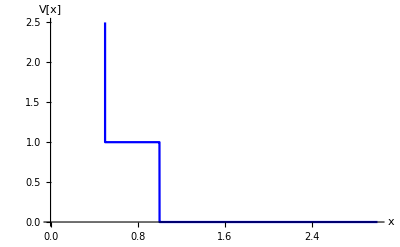

```mathematica
Plot[Subscript[V, val][x]/.{∞->1000},{x,0,3},AxesLabel->{"x","V[x]"},PlotStyle->Blue]
```

```mathematica
(* pressure *)
Subscript[p, val]=6/5;
N[%]
```

1.2

```mathematica
(* inverse temperature *)
Subscript[β, val]=2;
```

```mathematica
Subscript[c, sound]=csq[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}]^(1/2)
```

1.74264

```mathematica
Subscript[ω, val]={-Subscript[c, sound],0,Subscript[c, sound]};
```

```mathematica
(* symbolic formula for mean length (or elongation) *)
ellSym[p_,β_,{c_,d_,h_}]:=Module[{q=p β},1/q+c+(d-c)(1+ⅇ^((d-c) q)/(ⅇ^(h β)-1))^-1]
```

```mathematica
(* concrete value *)
FullSimplify[ellSym[Subscript[p, val],Subscript[β, val],{1/2,1,1}]]
N[%]
(* compare *)
%-ell[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}]
```

11/12+(-1+ⅇ^2)/(2 (-1+ⅇ^(6/5)+ⅇ^2))

1.24569

-3.40695×10^-10

```mathematica
(* symbolic formula for mean energy *)
enSym[p_,β_,{c_,d_,h_}]:=Module[{q=p β},h(1-(1+ⅇ^(-h β)(ⅇ^((d-c)q)-1))^-1)+1/(2 β)]
```

```mathematica
(* concrete value *)
FullSimplify[enSym[Subscript[p, val],Subscript[β, val],{1/2,1,1}]]
N[%]
(* compare *)
%-En[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}]
```

5/4+1/(-1+1/ⅇ^2-1/ⅇ^(4/5))

0.488961

3.79941×10^-12

```mathematica
(* "rotation" matrix R *)
Subscript[Rmat, val]=R[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}];
%//MatrixForm
```

(-0.806692 | -1. | 0.779958
2.10308 | 0. | 1.75256
-0.806692 | 1. | 0.779958)

```mathematica
(* inverse "rotation" matrix R^-1 *)
Subscript[Rinvmat, val]=Rinv[{Subscript[V, val],Subscript[p, val],Subscript[β, val]}];
%//MatrixForm
```

(-0.286921 | 0.255382 | -0.286921
-0.5 | 0. | 0.5
0.344305 | 0.264135 | 0.344305)

```mathematica
(* check *)
Norm[Subscript[Rinvmat, val].Subscript[Rmat, val]-IdentityMatrix[3]]
```

7.12121×10^-16

```mathematica
(* pointwise squares *)
Subscript[Rinvmat, val]^2//MatrixForm
```

(0.0823235 | 0.0652198 | 0.0823235
0.25 | 0. | 0.25
0.118546 | 0.0697672 | 0.118546)

```mathematica
(* G matrices *)
```

```mathematica
Subscript[G, -1]=Table[G[-1,i,j,{Subscript[V, val],Subscript[p, val],Subscript[β, val]}],{i,-1,1},{j,-1,1}];
Subscript[G, -1]//MatrixForm
```

(-0.366448 | 0.0123041 | -0.366448
0.0123041 | -0.20143 | 0.0123041
-0.366448 | 0.0123041 | 0.313147)

```mathematica
Subscript[G, 0]=Table[G[0,i,j,{Subscript[V, val],Subscript[p, val],Subscript[β, val]}],{i,-1,1},{j,-1,1}];
Subscript[G, 0]//MatrixForm
```

(-0.763523 | 0 | 0.
0 | 0 | 0
0. | 0 | 0.763523)

```mathematica
Subscript[G, 1]=Table[G[1,i,j,{Subscript[V, val],Subscript[p, val],Subscript[β, val]}],{i,-1,1},{j,-1,1}];
Subscript[G, 1]//MatrixForm
```

(-0.313147 | -0.0123041 | 0.366448
-0.0123041 | 0.20143 | -0.0123041
0.366448 | -0.0123041 | 0.366448)

```mathematica
(* check: Subscript[G, -1] == -AntiTranspose[Subscript[G, 1]] *)
Norm[Subscript[G, -1]+Table[Subscript[G, 1]⟦2-j,2-i⟧,{i,-1,1},{j,-1,1}]]
```

0.

```mathematica
(* Eq. (4.7) in "Nonlinear fluctuating hydrodynamics for anharmonic chains" *)
Subscript[λ, s]=2 √2 Abs[Subscript[G, 1]⟦3,3⟧]
```

1.03647

## Evaluate equilibration

```mathematica
(* exact "average" by construction (up to numerical precision) *)
Subscript[avr, 0]=Import["microcanonical_test_avr0.dat","Real64"]
Subscript[avr, 1]=Import["microcanonical_test_avr1.dat","Real64"]
```

{1.24569,3.91622×10^-19,0.488961}

{1.24569,3.91622×10^-19,0.488961}

```mathematica
Subscript[sqrs, val]=Partition[Partition[Import["microcanonical_test_sqrs.dat","Real64"],3],3];
Dimensions[%]
```

{16,3,3}

```mathematica
(* calculate covariance matrix *)
Subscript[S, mat]=#-KroneckerProduct[Subscript[avr, 0],Subscript[avr, 1]]&/@Subscript[sqrs, val];
Dimensions[%]
```

{16,3,3}

```mathematica
(* sum should be zero due to conservation laws *)
Norm[Total[Subscript[S, mat]]]
```

9.84581×10^-11

```mathematica
(* example: Subscript[r, j] correlation *)
Subscript[S, mat]⟦1;;5,1,1⟧
```

{0.217494,-0.0144895,-0.0144852,-0.0145979,-0.0146559}

```mathematica
(* example: Subscript[p, j] correlations *)
Subscript[S, mat]⟦;;,2,2⟧
```

{0.487229,-0.0324466,-0.031838,-0.0330056,-0.032759,-0.0321368,-0.0327006,-0.0322828,-0.0328899,-0.0322828,-0.0327006,-0.0321368,-0.032759,-0.0330056,-0.031838,-0.0324466}

```mathematica
(* example: Subscript[e, j] correlations *)
Subscript[S, mat]⟦;;,3,3⟧
```

{0.285395,-0.0187341,-0.019236,-0.0190179,-0.0189891,-0.0190729,-0.0188737,-0.0190542,-0.0194392,-0.0190542,-0.0188737,-0.0190729,-0.0189891,-0.0190179,-0.019236,-0.0187341}

```mathematica
(* example: Subscript[r, j]-Subscript[p, j] correlations *)
Subscript[S, mat]⟦;;,1,2⟧
```

{-0.0000217936,0.000316893,-0.000299863,0.000154925,0.0003334,-0.00033271,-0.000198698,0.0002137,0.000173539,-0.000117911,-0.000230123,-0.000409402,0.000234224,-0.00020981,0.000116407,0.000277223}

## Visualize results

```mathematica
Subscript[plt, label]="shoulder V, N="<>ToString[Length[Subscript[S, mat]]]<>", p="<>ToString[N[Subscript[p, val]]]<>", β="<>ToString[Subscript[β, val]]<>", c="<>ToString[Subscript[c, sound]]<>", runs=10^5";
```

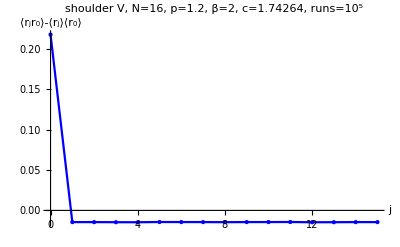

```mathematica
ListLinePlot[Transpose[{Range[0,Length[Subscript[S, mat]]-1],Subscript[S, mat]⟦;;,1,1⟧}],PlotLabel->Subscript[plt, label],PlotRange->All,Mesh->All,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"j","⟨r_jr_0⟩-⟨r_j⟩⟨r_0⟩"}]
Export[FileBaseName[NotebookFileName[]]<>"_r_corr.pdf",%];
```

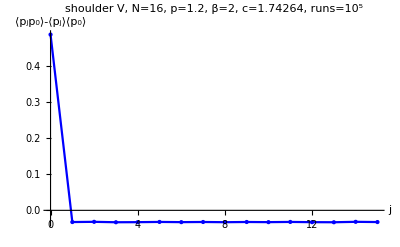

```mathematica
ListLinePlot[Transpose[{Range[0,Length[Subscript[S, mat]]-1],Subscript[S, mat]⟦;;,2,2⟧}],PlotLabel->Subscript[plt, label],PlotRange->All,Mesh->All,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"j","⟨p_jp_0⟩-⟨p_j⟩⟨p_0⟩"}]
Export[FileBaseName[NotebookFileName[]]<>"_p_corr.pdf",%];
```

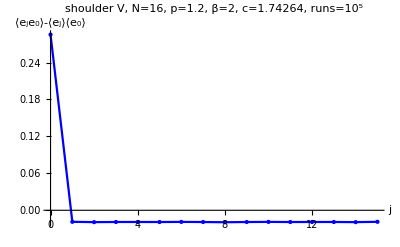

```mathematica
ListLinePlot[Transpose[{Range[0,Length[Subscript[S, mat]]-1],Subscript[S, mat]⟦;;,3,3⟧}],PlotLabel->Subscript[plt, label],PlotRange->All,Mesh->All,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"j","⟨e_je_0⟩-⟨e_j⟩⟨e_0⟩"}]
Export[FileBaseName[NotebookFileName[]]<>"_e_corr.pdf",%];
```